```mathematica
ClearAll["Global`*"]

(* Script outputs a rational polynomial fit of thermodynamic variables given by lattice qcd eos *)
(* Run cform.sh and then copy-paste fits to equation_of_state class functions in rhic/src/EquationOfState.cpp *)

(* Functions in equation_of_state class (no argument means it's a function of energy density)*)

(* Lattice QCD functions *)
(* equilbrium_pressure *)
(* speed_of_sound_squared() *)
(* effective_temperature()  *)

(* Quasiparticle functions *)
(* z_quasi() *)
(* mdmde_quasi() *)
(* equilibrium_mean_field() *)

(* Shear-bulk relaxation time coefficients. Where/how did I compute these? *)
(* beta_shear(T) *)
(* beta_bulk(T) *)

(* This is in rhic/src/EquationOfState.cpp but not part of equation_of_state class *)
(* equilibrium_energy_density(T) *)

Nf=3;
eg=16.Pi^2/30.;
eq=6.*3*7Pi^2/120.;  (*check these later*)
sFac = eg+eq 

(* plot styles *)
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

(* rational polynomial fit module *)
rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];


wd=SetDirectory@NotebookDirectory[];
eosData=Import[wd<>"/eos_hotqcd_smash.dat"];
```

15.6269

563.822

168.334

T min = 0.247529 fm^-1 or 0.0488442 GeV

T max = 5.07585 fm^-1 or 1.0016 GeV

energy min = 0.00174018 fm^-4

energy max = 9700.53 fm^-4

pressure min = 0.000358146 fm^-4

pressure max = 3119.57 fm^-4

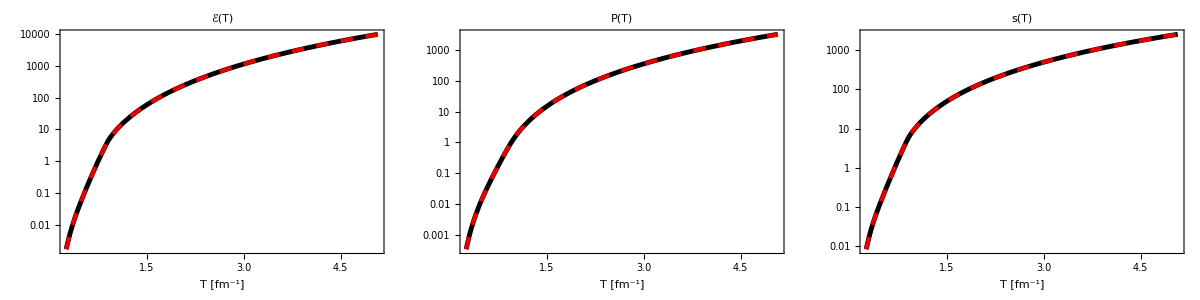

```mathematica
(* Hot QCD + Smash EoS data columns *)
(* T = [0.050 GeV, 1.0 GeV] *)

(* 1 = e  [GeV.fm^-3] *)
(* 2 = p  [GeV.fm^-3] *)
(* 3 = s  [fm^-3] *)
(* 4 = T  [GeV]  *)

(* convert all GeV units to fm^-1 *)
GeVtoInversefm =  1./0.197326938;  
energy= GeVtoInversefm *eosData[[All,1]];
pressure=GeVtoInversefm *eosData[[All,2]];
entropy=eosData[[All,3]];
temp =GeVtoInversefm * eosData[[All,4]];
Export["beta_coefficients/temperature.dat",Join[{Length[temp]},temp]];

Tmin=temp[[1]];
Tmax=temp[[-1]];
etemp1=Interpolation[Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}]];
Ptemp1=Interpolation[Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}]];
Sfit1=Interpolation[Table[{temp[[i]],entropy[[i]]},{i,1,Length[temp]}]];
(* check whether entropy density makes sense to old eos *)
etemp=etemp1;
Ptemp=Ptemp1;

(* the data file is too big. do uniform ΔT = 0.5 MeV intervals *)
(*temp=Table[GeVtoInversefm(0.05+0.0005*i),{i,0,1900}];*)
(*temp=Table[GeVtoInversefm(0.05+0.001*i),{i,0,950}];
energy=Table[etemp1[temp[[i]]],{i,1,Length[temp]}];
pressure=Table[Ptemp1[temp[[i]]],{i,1,Length[temp]}];

etemp=Interpolation[Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}]];
Ptemp=Interpolation[Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}]];*)
(*Sfit=Interpolation[Table[{temp[[i]],Sfit1[temp[[i]]]},{i,1,Length[temp]}]];*)
(*Sfit[T_]:=(etemp[T]+Ptemp[T])/T;*)

emin=etemp[Tmin];
emax=etemp[Tmax];
etemp[0.5*GeVtoInversefm]
Ptemp[0.5*GeVtoInversefm]
Print["T min = ",Tmin," fm^-1 or ",Tmin/GeVtoInversefm," GeV"]
Print["T max = ",Tmax," fm^-1 or ",Tmax/GeVtoInversefm," GeV"]
Print[]
Print["energy min = ",etemp[Tmin]," fm^-4"]
Print["energy max = ",etemp[Tmax]," fm^-4"]
Print[""]
Print["pressure min = ",Ptemp[Tmin]," fm^-4"]
Print["pressure max = ",Ptemp[Tmax]," fm^-4"]

(* Check that the modified functions are the same *)
Grid[{{LogPlot[{etemp[T],etemp1[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogPlot[{Ptemp[T],Ptemp1[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogPlot[{Sfit1[T],(etemp[T]+Ptemp[T])/T},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["s(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.00174018	0.00160671

567.583		567.583

9700.53		9700.53

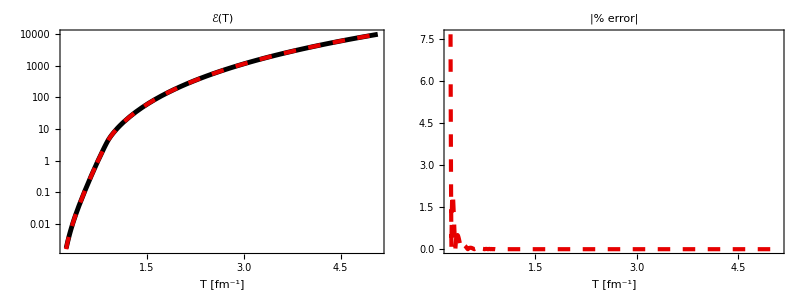

```mathematica
(*** e(T) fit ***)
edata=Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}];
n =18;
efit[T_]=rationalPolyFit[edata,n,n]/.{x->T};

Print[etemp[Tmin],"\t",efit[Tmin]]
Print[etemp[Tmax/2],"\t\t",efit[Tmax/2]]
Print[etemp[Tmax],"\t\t",efit[Tmax]]

Grid[{{
LogPlot[{etemp[T],efit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{100*Abs[(etemp[T]-efit[T])/etemp[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["energy.txt",CForm[efit[T]]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.000358146	0.00033065

169.51		169.51

3119.57		3119.57

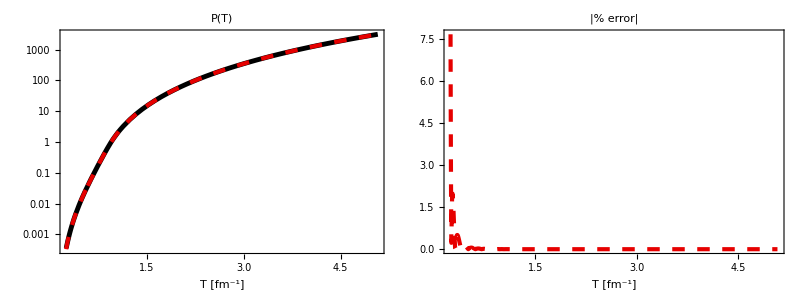

```mathematica
(*** P(T) fit ***)
pdata=Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}];
n =12;
Pfit[T_]=rationalPolyFit[pdata,n,n]/.{x->T};

Print[Ptemp[Tmin],"\t",Pfit[Tmin]]
Print[Ptemp[Tmax/2],"\t\t",Pfit[Tmax/2]]
Print[Ptemp[Tmax],"\t\t",Pfit[Tmax]]

Grid[{{
LogPlot[{Ptemp[T],Pfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{100*Abs[(Ptemp[T]-Pfit[T])/Ptemp[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["pressure.txt",CForm[Pfit[T]]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

0.223461	0.223449

0.312689		0.31269

0.325737		0.325735

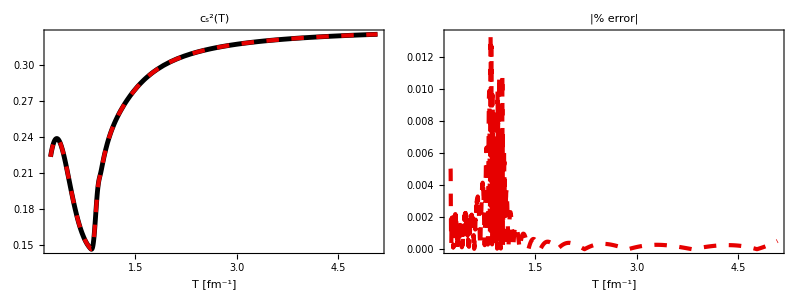

```mathematica
(*** Subscript[c, s]^2(T) fit ***)
(* Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= s/(de/dT) *)

cs2temp[T_]=Sfit1[T]/etemp'[T];
cs2data=Table[{temp[[i]],cs2temp[temp[[i]]]},{i,1,Length[temp]}];
n =18;
cs2fit[T_]=rationalPolyFit[cs2data,n,n]/.{x->T};

Print[cs2temp[Tmin],"\t",cs2fit[Tmin]]
Print[cs2temp[Tmax/2],"\t\t",cs2fit[Tmax/2]]
Print[cs2temp[Tmax],"\t\t",cs2fit[Tmax]]

Grid[{{
Plot[{cs2temp[T],cs2fit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{100*Abs[(cs2temp[T]-cs2fit[T])/cs2temp[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["cs2.txt",CForm[cs2fit[T]]];
```

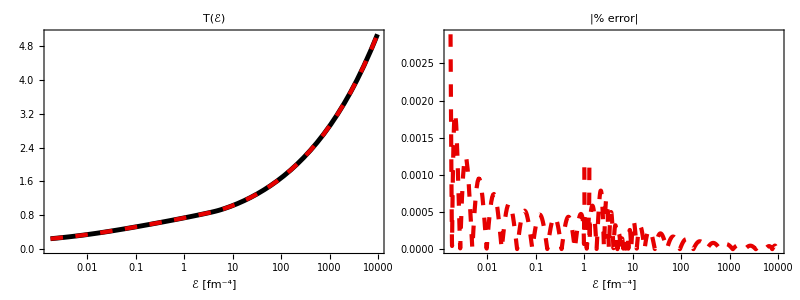

```mathematica
(*** T(e) fit ***)

Tdata=Table[{etemp[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];
Tfunc=Interpolation[Tdata];

n =18;
Tfit[e_]=rationalPolyFit[Tdata,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{100*Abs[(Tfunc[e]-Tfit[e])/Tfunc[e]]},{e,emin,emax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["temperature.txt",CForm[Tfit[e]]];
```

0.791709

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

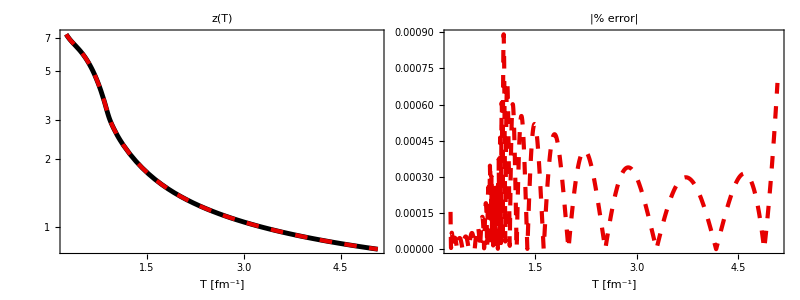

```mathematica
(*** z(e) fit ***)

Nc = 3.0;
g =Pi^4/180.0*(4.*(Nc^2-1.)+7.0*Nc*Nf);
F[T_]=(2.*Pi^2)/g*Sfit1[T]/T^3;

zStart=0.79;
zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];
zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[-1]]],{x,zStart},MaxIterations->5000];
zQuasi[[-1,2]]
For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]
zQuasifunc=Interpolation[zQuasi];

n =14;
zQuasifit[T_]=rationalPolyFit[zQuasi,n,n]/.{x->T};

Grid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["z(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{100*Abs[(zQuasifunc[T]-zQuasifit[T])/zQuasifunc[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["zquasi.txt",CForm[zQuasifit[T]]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

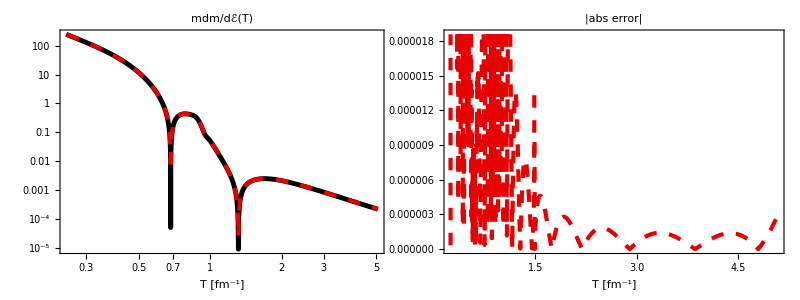

```mathematica
(*** m dm/de(T) fit ***) 

mQuasifunc[T_] =T*zQuasifunc[T]; 
mdmde[T_]=(mQuasifunc[T]*mQuasifunc'[T])/etemp'[T];
mdmdedata=Table[{temp[[i]],mdmde[temp[[i]]]},{i,1,Length[temp]}];

n =22;
mdmdefit[T_]=rationalPolyFit[mdmdedata,n,n]/.{x->T};

Grid[{{LogLogPlot[{Abs[mdmde[T]],Abs[mdmdefit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["mdm/dℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{Abs[(mdmde[T]-mdmdefit[T])]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|abs error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["mdmde.txt",CForm[mdmdefit[T]]];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

-4.83728

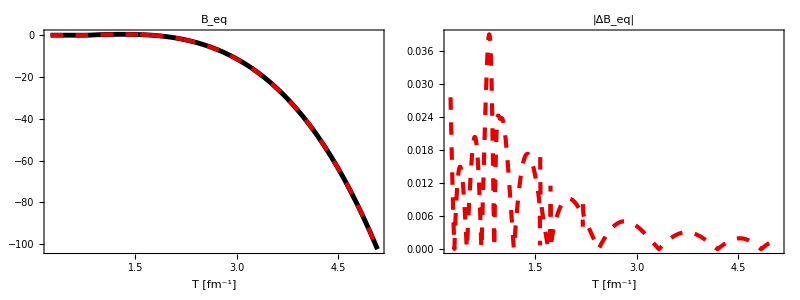

```mathematica
(*** Subscript[B, eq](T) fit ***)

Pquasi[T_]=(g*T^4)/(2.*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]]; (* equilibrium kinetic pressure *)
Beq=Table[{temp[[i]],Pquasi[temp[[i]]]-Ptemp[temp[[i]]]},{i,1,Length[temp]}];
Beqfunc=Interpolation[Beq];

n=14;
Beqfit[T_]=rationalPolyFit[Beq,n,n]/.{x->T};

Beqfunc[Tmax/2]

Grid[{{
Plot[{Beqfunc[T],Beqfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Beqfunc[T]-Beqfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["Beq.txt",CForm[Beqfit[T]]];
```

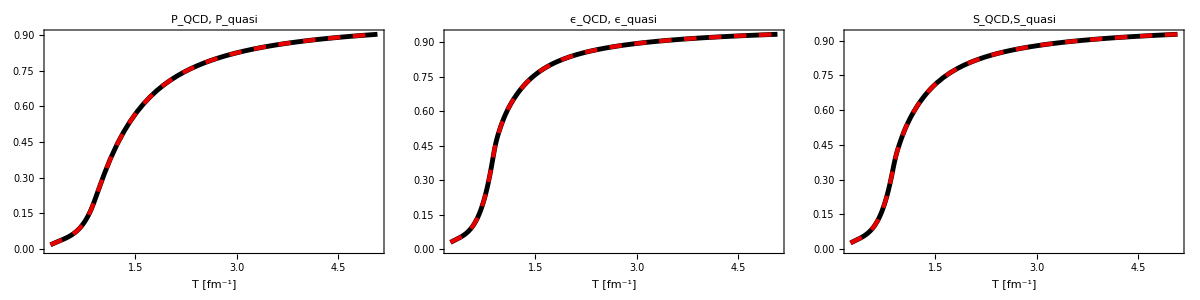

```mathematica
(* check thermodynamic consistency *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -Beqfunc[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+Beqfunc[T];
SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{Ptemp[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)(*,Beqfunc[T]/(sFac T^4/3),(Pquasi[T]+Beqfunc[T])/(sFac T^4/3)*)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{etemp[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Sfit1[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

134.589

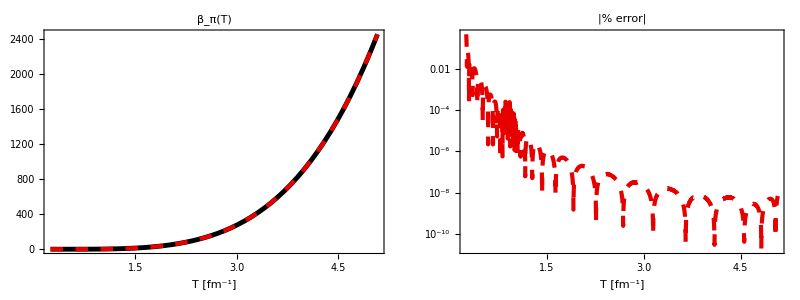

```mathematica
wd=SetDirectory@NotebookDirectory[];
betapiData=Import[wd<>"/beta_coefficients/results/betapi.dat"];
betapi = Interpolation[betapiData];
GeVtoInversefm =  1./0.197326938;  
n = 18;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapi[0.5*GeVtoInversefm]
Grid[{{Plot[{betapi[T],betapifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogPlot[{100*Abs[(betapi[T]-betapifit[T])/betapi[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|% error|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["betapi.txt",CForm[betapifit[T]]];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

1.81005

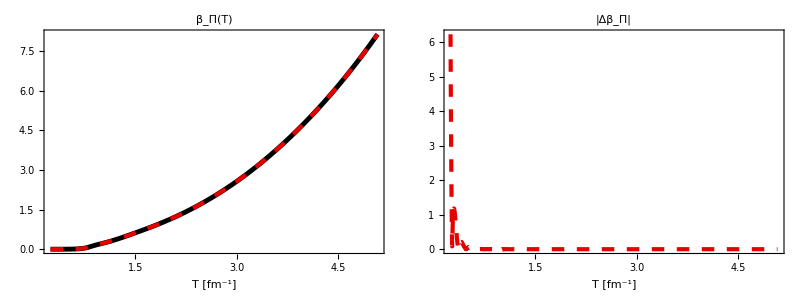

```mathematica
(* betabulk =5/3*betapi - cs2*(e+p) + cs2 * mdmdT*I11 *)
I11 = Interpolation[Import[wd<>"/beta_coefficients/results/betabulk.dat"]];
betabulk[T_]=5./3.*betapi[T]+cs2temp[T]*(mQuasifunc[T]*mQuasifunc'[T]*I11[T] - (etemp[T]+Ptemp[T]));
betabulkData=Table[{temp[[i]],betabulk[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};
betabulk[0.5*GeVtoInversefm]
Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(betabulk[T]-betabulkfit[T])/betabulk[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["betabulk.txt",CForm[betabulkfit[T]]];
```

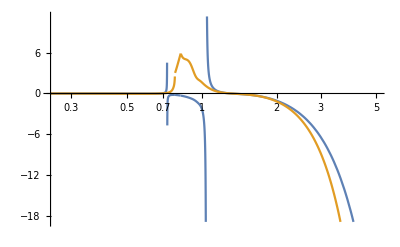

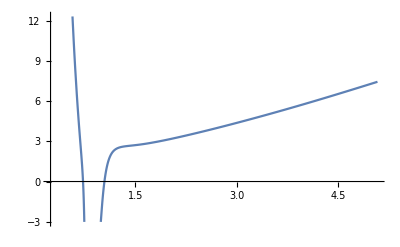

```mathematica
Tp = 0.155*GeVtoInversefm;
(* x = T / Tp *)

zetas[x_]:=Piecewise[{{0.9*Exp[-(x-1.)/0.025]+0.25*Exp[-(x-1.)/0.13]+0.001, x>1.05},{-13.77*x*x+27.55*x-13.45, 0.995≤ x≤ 1.05},{0.9*Exp[(x-1.)/0.0025]+0.22*Exp[(x-1.)/0.022]+0.03, x<0.995}}]


t0=0.25;
plptratio=1.0;

PL[T_]:=(etemp[T]*plptratio)/(2.+plptratio);
PT[T_]:=etemp[T]/(2.+plptratio);
mdot[T_]:=(-mdmde[T]*(etemp[T]+PL[T]))/(mQuasifunc[T]*t0);
bulk[T_]:=(2.*PT[T]+PL[T])/3.-Ptemp[T];
taubulk[T_]:=(zetas[T/Tp]*Sfit1[T])/betabulk[T];

dBasy[T_]:=(3.0*taubulk[T]*mdot[T]*bulk[T])/(mQuasifunc[T]-4.*taubulk[T]*mdot[T]);

dB2[T_]:=(-3.*taubulk[T]*mdmde[T]*bulk[T])/mQuasifunc[T]^2*(etemp[T]+Ptemp[T])/t0;

LogLinearPlot[{dBasy[T],dB2[T]},{T,Tmin,Tmax}]
Plot[mQuasifunc[T]-4.*taubulk[T]*mdot[T],{T,Tmin,Tmax}]
```

```mathematica
T0=0.5*GeVtoInversefm;
etemp[T0]
PL[T0]
Beqfunc[T0]
dBasy[0.5*GeVtoInversefm]
mQuasifunc[T0]
mdmde[T0]
zetas[T0/Tp]
betabulk[T0]
taubulk[T0]
```

```mathematica
zetas[x_]:=Piecewise[{{0.9*Exp[-(x-1.)/0.025]+0.25*Exp[-(x-1.)/0.13]+0.001, x>1.05},{-13.77*x*x+27.55*x-13.45, 0.995≤ x≤ 1.05},{0.9*Exp[(x-1.)/0.0025]+0.22*Exp[(x-1.)/0.022]+0.03, x<0.995}}]


Clear[t0]
Tp = 0.155*GeVtoInversefm;
(* x = T / Tp *)

PL[T_,ratio_]:=(etemp[T]*ratio)/(2.+ratio);
mdot[T_,ratio_,t0_]:=(-mdmde[T]*(etemp[T]+PL[T,ratio]))/(mQuasifunc[T]*t0);
bulk[T_]:=etemp[T]/3.-Ptemp[T];
taubulk[T_]:=(zetas[T/Tp]*Sfit1[T])/betabulk[T];

dBasy[T_,ratio_,t0_]:=(3.*taubulk[T]*mdot[T,ratio,t0]*bulk[T])/(mQuasifunc[T]-4.*taubulk[T]*mdot[T,ratio,t0]);

dB2[T_,t0_]:=(-3.*taubulk[T]*mdmde[T]*bulk[T])/mQuasifunc[T]^2*(etemp[T]+Ptemp[T])/t0;

Manipulate[LogLinearPlot[{dBasy[T,ratio,t0],dB2[T,t0]},{T,Tmin,Tmax},PlotRange->{-20,20},ImageSize->600],{{t0,0.25},0.25,5.25,0.05},{{ratio,1},0,1,0.05}]
```